# Math 385 HW # 6

## Mario L Gutierrez Abed

(1) Construct a polynomial interpolation p(x) using Vandermonde’s process (use degree 3). The interpolation points are x=4,5,6,7. The function is  f(x)=x^2 ⅇ^-x-1/10.

```mathematica
f[x_]=x^2 ⅇ^-x-1/10;
pts = {4,5,6,7};
vandmat=({{1, pts⟦1⟧, (pts⟦1⟧)^2, (pts⟦1⟧)^3}, {1, pts⟦2⟧, (pts⟦2⟧)^2, (pts⟦2⟧)^3}, {1, pts⟦3⟧, (pts⟦3⟧)^2, (pts⟦3⟧)^3}, {1, pts⟦4⟧, (pts⟦4⟧)^2, (pts⟦4⟧)^3}});
yvec=({{f[pts⟦1⟧]}, {f[pts⟦2⟧]}, {f[pts⟦3⟧]}, {f[pts⟦4⟧]}});
sol=LinearSolve[vandmat,yvec];
blah={1,x,x^2,x^3}.sol;
p[x_]=blah⟦1⟧
```

-1/10-980/ⅇ^7+2520/ⅇ^6-2100/ⅇ^5+560/ⅇ^4+(1813/(3 ⅇ^7)-1494/ⅇ^6+1175/ⅇ^5-856/(3 ⅇ^4)) x+(-245/(2 ⅇ^7)+288/ⅇ^6-425/(2 ⅇ^5)+48/ⅇ^4) x^2+((49-108 ⅇ+75 ⅇ^2-16 ⅇ^3) x^3)/(6 ⅇ^7)

(2) Construct a 3^rd degree Taylor expansion t(x) based about x_0=5.

```mathematica
Subscript[f, 1][x_]=D[f[x],x];
Subscript[f, 2][x_]=D[f[x],{x,2}];
Subscript[f, 3][x_]=D[f[x],{x,3}];
t[x_]=f[5]+Subscript[f, 1][5]*(x-5)+1/2 Subscript[f, 2][5]*(x-5)^2+1/6 Subscript[f, 3][5]* (x-5)^3
```

-1/10+25/ⅇ^5-(15 (-5+x))/ⅇ^5+(7 (-5+x)^2)/(2 ⅇ^5)-(-5+x)^3/(6 ⅇ^5)

(3) Graph all threef(x),p(x),t(x) on the same plot using different colors.

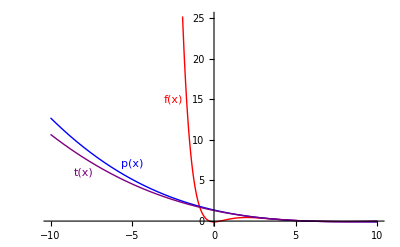

```mathematica
Plot[{f[x],p[x],t[x]},{x,-10,10},PlotStyle->{Red,Blue,Purple},Prolog->{Red,Text["f(x)",{-2.5,15}],Blue,Text["p(x)",{-5,7}],Purple,Text["t(x)",{-8,6}]}]
```

As expected both polynomials fit very well the function f(x) in the domain where we approximated it [4,7]. Let’s take a closer look at this interval :

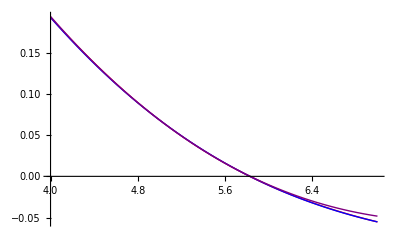

```mathematica
Plot[{f[x],p[x],t[x]},{x,4,7},PlotStyle->{Red,Blue,Purple}]
```

We can see that they are pretty much identical. 

(4) Calculate norm error and mean norm error for p(x) and  t(x). 
▸ Norm error:

```mathematica
√(∫_4^7 (f[x]-p[x])^2 ⅆx)//N
√(∫_4^7 (f[x]-t[x])^2 ⅆx)//N
```

0.000485493

0.00354151

▸ Mean norm error:

```mathematica
1/(7-4)√(∫_4^7 (f[x]-p[x])^2 ⅆx)//N
1/(7-4)√(∫_4^7 (f[x]-t[x])^2 ⅆx)//N
```

0.000161831

0.0011805